## Initialisation stuff

```mathematica
Needs["QDENSITY`Qdensity`"];
packageDir =FileNameJoin[{ NotebookDirectory[],"QSIM"}];
Needs["QSIM`noise`",FileNameJoin[{packageDir,"QSIM_noise.m"}]]
```

```mathematica
?QDENSITY`Qdensity`*
```

```mathematica
CombineErrors[errorTable_]:=Module[{x,probNone},probNone=Times@@((1-#)&/@errorTable);
Total[Table[probNone errorTable[[ii]]/(1-errorTable[[ii]]),{ii,1,Length[errorTable]}]]](*for small probabilities, these depolarizing channels just add up.*)
PZ[i_]:=Switch[i,0,Subscript[𝒫, 0],1,Subscript[𝒫, 1]];
projectors={PX,PY,PZ};
KP[r__]:=KroneckerProduct[r];
phi0={{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}};
id =𝕀;
bellState[i_]:=ArrayFlatten[Outer[Times,PauliMatrix[i],PauliMatrix[0]]].phi0.ArrayFlatten[Outer[Times,PauliMatrix[i],PauliMatrix[0]]];
```

```mathematica
findFileInDataDir[string_,dataDir_,daysPreviousToSearch_:365]:=Module[{filenames,daysPrevious},daysPrevious=0;While[(daysPrevious<daysPreviousToSearch) &&( Length[filenames]==0),filenames=Select[FileNames["*"<>string<>"*",FileNameJoin[{dataDir,DateString[AbsoluteTime[]-86400 daysPrevious,{"Year","Month","Day"}]}]],DirectoryQ];daysPrevious++;];Return[filenames]]

GetDirectoryNameContaining::notunique="File not unique";
GetDirectoryNameContaining::nofile="No matching file found";
GetDirectoryNameContaining[string_,dir_:NotebookDirectory[],searchDataDir_:True]:=Module[{filenames},If[searchDataDir==False,filenames=Select[FileNames["*"<>string<>"*",dir],DirectoryQ];,filenames=findFileInDataDir[string,dir]];
Which[Length[filenames]==1,Return[filenames[[1]]],Length[filenames]==0,Message[GetDirectoryNameContaining::nofile];Return[$Failed],Length[filenames]>0,Message[GetDirectoryNameContaining::notunique];Return[$Failed]]]

GetCorrelationFile[string_,dir_:NotebookDirectory[]]:=
Import[FileNameJoin[{GetDirectoryNameContaining[string,dir],"correlations.h5"}],{"Datasets",{"/correlations","/correlations_u","/norm_correlators","/norm_correlators_u","/counts_per_pt"}}]
```

```mathematica
GetMsmtFilenameContaining::notunique="File not unique";
GetMsmtFilenameContaining::nofile="No matching file found";
GetMsmtFilenameContaining[string_,dir_:NotebookDirectory[]]:=Module[{filenames,dirname},dirname=GetDirectoryNameContaining[string,dir];
Return[FileNameJoin[{dirname,FileNameSplit[dirname][[-1]]<>".hdf5"}]];]

GetAdwinGroup[filename_]:=Module[{groups,group,x},
groups=StringSplit[Import[filename,"Groups"],"/"];
For[x=1,x<=Length[groups],x++,group=groups[[x]];(Which[Length[group]==0,Null,group[[-1]]=="adwindata",Return["/"<>StringJoin[Riffle[group,"/"]]]])];
Return[$Failed]];

GetAdwinData[filename_,arrayname_]:=If[$VersionNumber≥10,Import[filename,{"Datasets",GetAdwinGroup[filename]<>"/"<>arrayname}],Import[filename,{"Datasets",GetAdwinGroup[filename]<>"/"<>arrayname}]];

GetPQData[filename_,arrayname_]:=Import[filename,arrayname];

GetMsmtAttribute[filename_,attribute_]:=
If[$VersionNumber≥10,(attribute)/.(Import[filename,{"Attributes",GetAdwinGroup[filename]}]),attribute/.((GetAdwinGroup[filename])/.Import[filename,{"Attributes"}])]

GetMsmtAttributeNames[filename_]:=
Keys[Import[filename,{"Attributes",GetAdwinGroup[filename]}]];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
CreateDataPlotLists[plotpoints_,data_,error_]:=({{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@Transpose[Join[{plotpoints},#]])&/@Transpose@{Transpose[data],Transpose[error]}

FidFromData[XX_,ZZ_]:=(1+2 Abs[XX]+Abs[XX])/4;
FidErrorFromData[XXerror_,ZZerror_]:=Sqrt[(0.5XXerror)^2+(0.25ZZerror)^2];
CreateDataFidelityList[plotpoints_,dataXX_,errorXX_,dataZZ_,errorZZ_]:=({{#[[1]],FidFromData[#[[2]],#[[4]]]},ErrorBar[FidErrorFromData[#[[3]],#[[5]]]]}&/@Transpose[Join[{plotpoints},#]])&/@Transpose@{Transpose[dataXX],Transpose[errorXX],Transpose[dataZZ],Transpose[errorZZ]}

TailFromData[msmtFile_,corrs_]:=Module[{countedAWGreps,AWGrepsPerAttempt,sweepLength,nrofROsequences,repetitions,repsPerClick,filteredPointFraction},countedAWGreps=GetAdwinData[msmtFile,"counted_awg_reps"];
AWGrepsPerAttempt=countedAWGreps-Prepend[countedAWGreps[[;;-2]],0];
sweepLength = GetMsmtAttribute[msmtFile,"sweep_length"];nrofROsequences = GetMsmtAttribute[msmtFile,"nr_of_ROsequences"];
repetitions = Length[countedAWGreps]/(sweepLength nrofROsequences);
repsPerClick=N[Mean[ArrayReshape[AWGrepsPerAttempt,{repetitions,sweepLength}]]];
filteredPointFraction=N@(Total[corrs[[5]],{1}]/repetitions);
Return[10^4 filteredPointFraction/repsPerClick]]
```

#### Single qubit gates

```mathematica
(*Definition of single spin rotations using the qdensity package
Nomenclature:  r followed by a capital letter --> rotation by π around the axis specified by the letter.
			r followed by a lower case letter: rotation by π/2 around the axis specified by that letter
The rotation direction is given by the appended letter m or p*)

{rxp,rXp,ryp,rYp,rzp,rZp}=Table[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))],{j,1,6}];
```

## Model

Parameters that define the raw state (generated by a single photon click): 

vis - the visibility of the photons
fz  - determined by initialization error, MW pulse infidelity and spin flip probability  
r  - the proportion of the state in the unentangled ‘11’ state

The r value depends on: 
pDetect - detection efficiency
theta  - the initial rotation of the state of the qubits: Cos[theta]|0> + Sin[theta]|1>
PDC - dark count prob per detector

the function rawState[fid_,pLoss_] generates a density matrix of the entangled state generated after a single detector click

```mathematica
rValue[theta_,pDetect1_,pDetect2_,pDC_]:=Module[{p00,p01,p10,p11,pd1,pd2},
pd1 = pDetect1;
pd2 = pDetect2;

p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd2+ 2*pDC*(1-pDC)*(1-pd2));
p10 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd1+ 2*pDC*(1-pDC)*(1-pd1));
p11 = Sin[theta]^4 *((1-pDC)^2*(pd1*(1-pd2)+pd2*(1-pd1)) + 2*(1-pDC)*pDC*(1-pd1)*(1-pd2));

{p00,p01,p10,p11}/(p00+p01+p10+p11)
]
```

#### Raw state generation

```mathematica
rawState[vis_,fz_,rValue_,RndOpticalPhase_]:=Chop[rValue[[1]]*KP[Subscript[𝒫, 1],Subscript[𝒫, 1]]+{{(1-fz)(rValue[[2]]+rValue[[3]])/2,0,0,0},{0,rValue[[2]]*fz,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[ⅈ*RndOpticalPhase],0},{0,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[-ⅈ*RndOpticalPhase],rValue[[3]]*fz,0},{0,0,0,(1-fz)(rValue[[2]]+rValue[[3]])/2}}+rValue[[4]]*KP[Subscript[𝒫, 0],Subscript[𝒫, 0]]];
```

```mathematica
PhaseErrorRawState[θ_,pDetect1_,pDetect2_,pDC_,vis_,fz_,pPhaseError_,zRotAngle_:0,opticalPhase_:0]:=(
DM = rawState[Sqrt[vis],fz,rValue[θ,pDetect1,pDetect2,pDC],opticalPhase];
(*include phase error due to interferometric instability*)
DM = KP[𝕀,RotZ[zRotAngle]].DM.KP[𝕀,RotZ[zRotAngle]]†;
DM = (1-pPhaseError)*DM + pPhaseError*KP[DiagonalMatrix[{1,1}],Subscript[σ, 3]].DM.(KP[DiagonalMatrix[{1,1}],Subscript[σ, 3]])†
)

FirstClickProb[theta_,pd1_,pd2_,pDC_:0] := (-1+pDC) (-2 pDC Cos[theta]^4+(-4 pDC+pd1 (-1+3 pDC)+pd2 (-1+3 pDC)) Cos[theta]^2 Sin[theta]^2-(pd2+pd1 (1+2 pd2 (-1+pDC)-5 pDC)+2 pDC+2 pd1^2 pDC-pd2 pDC) Sin[theta]^4);
CumProb[nMax_,theta_,pd1_,pd2_,pDC_:0]:=1-(1-FirstClickProb[theta,pd1,pd2,pDC] )^nMax
```

#### Plot function defs

```mathematica
PopulationToTheta[p_]:=ArcSin[Sqrt[p]]

GetFidelities[start_,stop_,steps_,rawState_]:=(
Table[
(Re@Fidelity[rawState[PopulationToTheta[i]],bellState[2]])^2,{i,start,stop,Abs[(start-stop)]/steps}
])

BasisList=Transpose[{{1,0,1,0},{1,1,0,0}}];
GetCorrs[start_,stop_,steps_,rawState_,j_]:=(
Table[
Re@Tr[rawState[PopulationToTheta[i]].KP[projectors[[j]][BasisList[[k,1]]],projectors[[j]][BasisList[[k,2]]]]],{k,1,4},{i,start,stop,Abs[(start-stop)]/steps}
])
GetSigmas[start_,stop_,steps_,rawState_]:=(
Table[
Re@Tr[rawState[PopulationToTheta[i]].KP[Subscript[σ, j],Subscript[σ, j]]],{j,2,3},{i,start,stop,Abs[(start-stop)]/steps}
])
GetFirstClickProbs[start_,stop_,steps_,pd1_,pd2_,pDC_:0]:=(
Table[
FirstClickProb[PopulationToTheta[i],pd1,pd2,pDC],{i,start,stop,Abs[(start-stop)]/steps}
]
)
GetSuccessRate[start_,stop_,steps_,pd1_,pd2_,pDC_:0]:=(
GetFirstClickProbs[start,stop,steps,pd1,pd2,pDC]*10^4
)
GetSuccessRateBK[start_,stop_,steps_,pDetect1_,pDetect2_]:=(
Table[pDetect1*pDetect2*10^4/2,{i,start,stop,Abs[start-stop]/steps}]
)
```

```mathematica
CreatePlotLists[func_,start_,stop_,steps_,args___]:=(
res = func[start,stop,steps,args];
plotLists={};
x = Table[i,{i,start,stop,Abs[(start-stop)]/steps}];
If[ArrayDepth[res]==1,plotLists=Partition[Riffle[x,res],2],
For[j=1,j<=Dimensions[res][[1]],
j++,
AppendTo[plotLists,Partition[Riffle[x,res[[j,;;]]],2]]]];
plotLists
)
```

```mathematica
divisionFunction[xMin_,xMax_]:=N@FindDivisions[{xMin,xMax},{8,5}];
gridFunction[xMin_,xMax_]:=First[divisionFunction[xMin,xMax]]
Options[tickFunction]={"MinorLength"->0.005,"MajorLength"->.01,"InsideOutside"->{1,0}};
tickFunction[xMin_,xMax_,OptionsPattern[]]:=Module[{major,minor},{major,minor}=divisionFunction[xMin,xMax];
Join[Map[{#,#,OptionValue["InsideOutside"] OptionValue["MajorLength"]}&,major],Map[{#,"",OptionValue["InsideOutside"] OptionValue["MinorLength"]}&,Flatten[minor[[All,2;;-2]]]]]]
tickFunctionNoLabel[xMin_,xMax_]:=Map[{#[[1]],"",#[[-1]]}&,tickFunction[xMin,xMax]]
```

```mathematica
col1 = ColorData[97,"ColorList"][[1]];
col2 = ColorData[97,"ColorList"][[2]];
col3 = ColorData[97,"ColorList"][[3]];
```

## Single click entanglement

### Load data

```mathematica
ZZstring="162145";
XXstring="160448";
ZZ=GetCorrelationFile[ZZstring,"X:\\data"];
XX=GetCorrelationFile[XXstring,"X:\\data"];
ZZmsmtFile=GetMsmtFilenameContaining[XXstring,"X:\\data"];
```

```mathematica
dataPoints=GetMsmtAttribute[ZZmsmtFile,"sweep_pts"];
```

### Simulate

```mathematica
xmin=0.0;
xmax=0.35;
vis =0.88;
fz = 0.99;
pDetect1 = 0.00016*1.9;
pDetect2 = 0.00032*1.9;
pDC=(0.0072+0.0126)/2*10^-4;
pDCb=20*30*^-9;
phaseStandardDevb =22(π/180); 
phaseStandardDev =22(π/180); 
phaseOffset=0π/180;
pPhaseError =1/2( 1-E^(-(1/2(phaseStandardDev^2))));
pPhaseErrorb =1/2( 1-E^(-(1/2(phaseStandardDevb^2))));
```

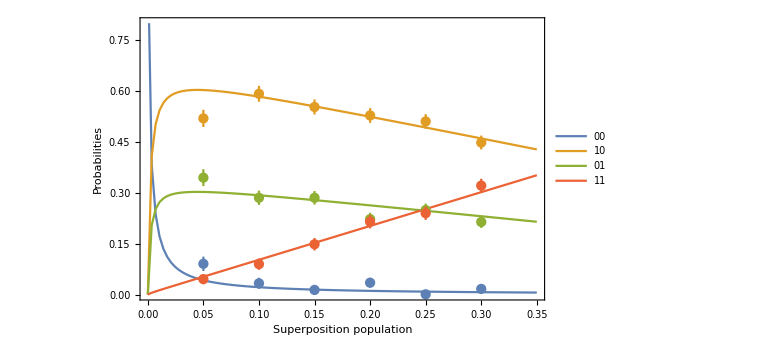

```mathematica
ZZCorrs=ListPlot[CreatePlotLists[GetCorrs,xmin,xmax,100,PhaseErrorRawState[#,pDetect1,pDetect2,pDC,Sqrt[vis],fz,pPhaseError,phaseOffset]&,3],Frame->True,PlotRange->{{xmin,xmax},{0,0.8}},FrameLabel->{"Superposition population","Probabilities"},PlotLegends->{"00","10","01","11"},Joined->True,LabelStyle-> Bold,ImageSize->Large];

ZZCorrsData=ErrorListPlot[CreateDataPlotLists[dataPoints,ZZ[[3]],ZZ[[4]]],Joined->False];
Show[{ZZCorrs,ZZCorrsData}]
```

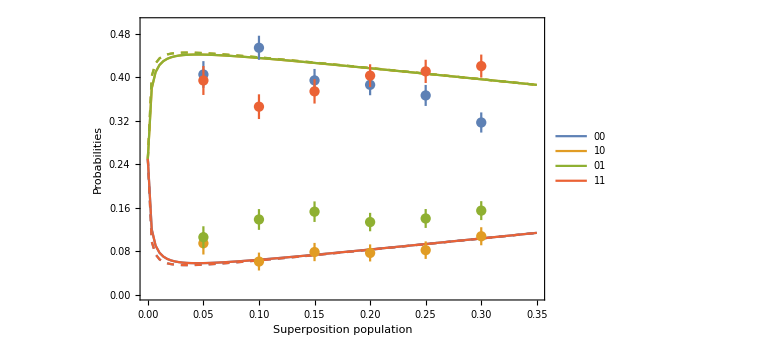

```mathematica
XXCorrs=ListPlot[CreatePlotLists[GetCorrs,xmin,xmax,100,PhaseErrorRawState[#,pDetect1,pDetect2,pDC,Sqrt[vis],fz,pPhaseError,phaseOffset]&,2],Frame->True,PlotRange->{{xmin,xmax},{0,0.5}},FrameLabel->{"Superposition population","Probabilities"},PlotLegends->{"00","10","01","11"},Joined->True,LabelStyle-> Bold,ImageSize->Large];

XXCorrsb=ListPlot[CreatePlotLists[GetCorrs,xmin,xmax,100,PhaseErrorRawState[#,pDetect1,pDetect2,pDCb,Sqrt[vis],fz,pPhaseErrorb,phaseOffset]&,2],Frame->True,PlotRange->{{xmin,xmax},{0,0.5}},PlotStyle->Dashed,FrameLabel->{"Superposition population","Probabilities"},Joined->True,LabelStyle-> Bold,ImageSize->300];

XXCorrsData=ErrorListPlot[CreateDataPlotLists[dataPoints,XX[[3]],XX[[4]]],Joined->False];
Show[{XXCorrs,XXCorrsb,XXCorrsData}]
```

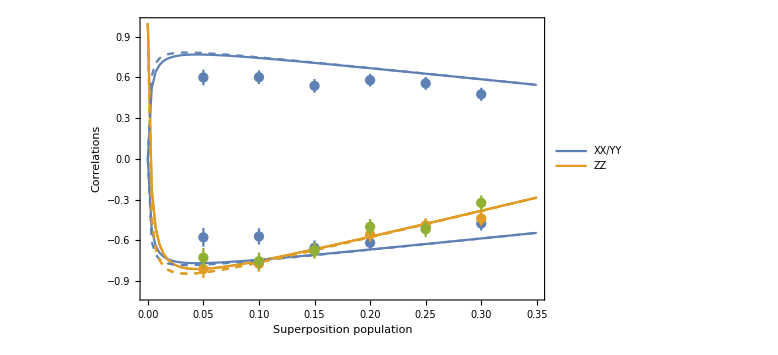

```mathematica
psi0=ListPlot[CreatePlotLists[GetSigmas,xmin,xmax,100,PhaseErrorRawState[#,pDetect1,pDetect2,pDC,Sqrt[vis],fz,pPhaseError,phaseOffset,0]&],Frame->True,PlotRange->{{xmin,xmax},{-1,1}},FrameLabel->{"Superposition population","Correlations"},PlotLegends->{"XX/YY","ZZ"},Joined->True,LabelStyle-> Bold,ImageSize->Large];

psi1=ListPlot[CreatePlotLists[GetSigmas,xmin,xmax,100,PhaseErrorRawState[#,pDetect1,pDetect2,pDC,Sqrt[vis],fz,pPhaseError,phaseOffset,π]&],Frame->True,PlotRange->{{xmin,xmax},{-1,1}},FrameLabel->{"Superposition population","Correlations"},Joined->True,LabelStyle-> Bold,ImageSize->300];

psi0b=ListPlot[CreatePlotLists[GetSigmas,xmin,xmax,100,PhaseErrorRawState[#,pDetect1,pDetect2,pDCb,Sqrt[vis],fz,pPhaseErrorb,phaseOffset,0]&],Frame->True,PlotStyle->Dashed,PlotRange->{{xmin,xmax},{-1,1}},FrameLabel->{"Superposition population","Correlations"},Joined->True,LabelStyle-> Bold,ImageSize->300];

psi1b=ListPlot[CreatePlotLists[GetSigmas,xmin,xmax,100,PhaseErrorRawState[#,pDetect1,pDetect2,pDCb,Sqrt[vis],fz,pPhaseErrorb,phaseOffset,π]&],Frame->True,PlotStyle->Dashed,PlotRange->{{xmin,xmax},{-1,1}},FrameLabel->{"Superposition population","Correlations"},Joined->True,LabelStyle-> Bold,ImageSize->300];

XXCorrData=ErrorListPlot[CreateDataPlotLists[dataPoints,XX[[1]],XX[[2]]],Joined->False,PlotStyle->{col1,col1}];

ZZCorrData=ErrorListPlot[CreateDataPlotLists[dataPoints,ZZ[[1]],ZZ[[2]]],Joined->False,PlotStyle->{col2,col3}];
Show[{psi0,psi1,psi0b,psi1b,XXCorrData,ZZCorrData}]
```

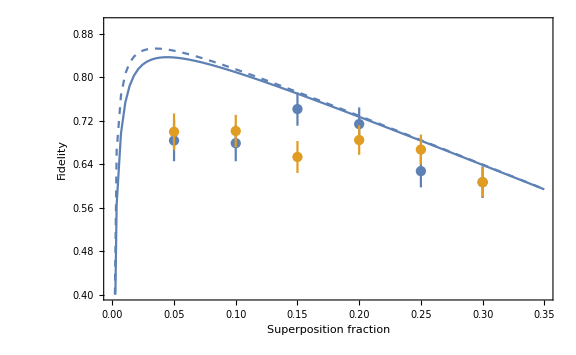
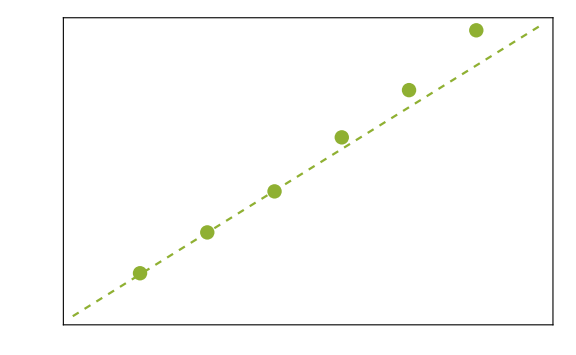

```mathematica
pltFidelity = ListPlot[CreatePlotLists[GetFidelities,xmin,xmax,100,PhaseErrorRawState[#,pDetect1,pDetect2,pDC,Sqrt[vis],fz,pPhaseError,phaseOffset]&],Frame->{True,True,True,False},PlotStyle->col1,FrameLabel->{"Superposition fraction","Fidelity"},FrameStyle->{Automatic,col1,Automatic,Automatic},PlotRange->{Automatic,{0.4,0.9}},Joined->True,LabelStyle-> Bold,ImagePadding->50,ImageSize->Large];

pltFidelityb = ListPlot[CreatePlotLists[GetFidelities,xmin,xmax,100,PhaseErrorRawState[#,pDetect1,pDetect2,pDCb,Sqrt[vis],fz,pPhaseErrorb,phaseOffset]&],Frame->{True,True,True,False},PlotStyle->Directive[col1,Dashed],FrameLabel->{"Superposition fraction","Fidelity"},FrameStyle->{Automatic,col1,Automatic,Automatic},PlotRange->{Automatic,{0.4,0.9}},Joined->True,LabelStyle-> Bold,ImagePadding->50,ImageSize->Large];

pltRate = ListPlot[{CreatePlotLists[GetSuccessRate,xmin,xmax,100,pDetect1,pDetect1,pDC]},Frame->{None,None,None,True},FrameStyle->{{None,col3},{None,None}},FrameLabel->{{"","Success probability (10^-4)"},{"",""}},LabelStyle-> Bold,Joined->True,PlotStyle->Directive[Dashed,col3],ImagePadding->50,FrameTicks->{{None,tickFunction},{None,None}},ImageSize->Large];

FidData=ErrorListPlot[CreateDataFidelityList[dataPoints,XX[[1]],XX[[2]],ZZ[[1]],ZZ[[2]]],Joined->False,PlotStyle->{col1,col2}];

tailData=ListPlot[Transpose[{dataPoints,TailFromData[ZZmsmtFile,ZZ]}],PlotStyle->Directive[PointSize[0.018],col3],PlotRange->{{xmin,xmax},Automatic}];

Overlay[{Show[{pltFidelity,pltFidelityb,FidData}],Show[{pltRate,tailData}]}]
```